```mathematica
Plot[Im[QGamma[1-2-σ,E^(2π I/k)]/QGamma[1-2+σ,E^(2π I/k)]/.{k->2}],{σ,0,1}]
```

-Graphics-

```mathematica
n=6;
qP[z_,q1_]:=Exp[Sum[-z^m/m*1/(1-q1^m),{m,1,n}]];
```

General::munfl: Exp[-6.76845×10^9] is too small to represent as a normalized machine number; precision may be lost.

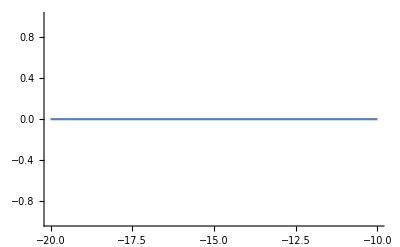

```mathematica
Plot[qP[q^(x+σ),q]/qP[q^(x-σ),q]/.{q->.8,x->2},{σ,-20,-10}]
```

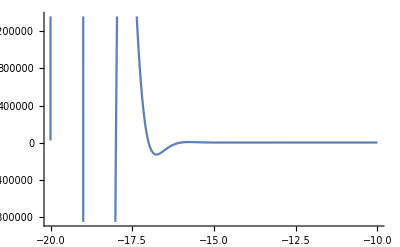

```mathematica
Plot[QPochhammer[q^(x+σ),q]/QPochhammer[q^(x-σ),q]/.{q->.8,x->2},{σ,-20,-10}]
```

```mathematica
(1-q)^(-2 σ) QGamma[1-x-σ,q]/QGamma[1-x+σ,q]//FunctionExpand
```

QPochhammer[q^(1-x+σ),q]/QPochhammer[q^(1-x-σ),q]

```mathematica
QGamma[ z,q]//FunctionExpand
```

((1-q)^(1-z) QPochhammer[q,q])/QPochhammer[q^z,q]

```mathematica
NSolve[1==QPochhammer[q^σ,q]/QPochhammer[q^-σ,q]/.{q->0.5,x->4},σ]
```

$Aborted

```mathematica
1/(1-q^3)/.q->E^(2 π I/3)
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
(q^σ-q^-σ)/.{q->E^(2 π I/k)}/.{k->3}//PowerExpand
```

-ⅇ^(-2/3 ⅈ π σ)+ⅇ^((2 ⅈ π σ)/3)

```mathematica
Series[1/(1-q^3),{q,E^(2 π I/3),0}]
```

-(-1)^(2/3)/(3 (q-ⅇ^((2 ⅈ π)/3)))+1/3+O[q-ⅇ^((2 ⅈ π)/3)]^1

```mathematica
E^0.00001
```

1.00001

```mathematica
(0.+6.283185307179586 ⅈ)
```

0.+6.28319 ⅈ

```mathematica
Reduce[0==Sum[(q^(m α)(q^(m σ)-q^(-m σ)))/(m(1-q^m)),{m,1,6}]/.{α->0.5,q->1 E^0.00001},σ]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈ℤ&&(σ==-100000. ((0.+3.14159 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==(0.-628319. ⅈ) C[1]||σ==-100000. ((0.681611+3.14159 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==-100000. ((-0.681611+3.14159 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==-100000. ((0.756697-1.98327 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==-100000. ((0.756697+1.98327 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==-100000. ((-0.756697-1.98327 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==-100000. ((-0.756697+1.98327 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==-100000. ((-0.717162-0.906514 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==-100000. ((-0.717162+0.906514 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==-100000. ((0.717162-0.906514 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==-100000. ((0.717162+0.906514 ⅈ)+(0.+6.28319 ⅈ) C[1]))

```mathematica
N[-1.9840528537628834-0.0012366387046158815 I,0]//Rationalize
```

-1.98405-0.00123664 ⅈ

```mathematica
6.25+0.1 I//Rationalize
```

25/4+ⅈ/10

```mathematica
Series[(q^(m α)(q^(m σ)-q^(-m σ)))/(m(1-q^m))/.q->E^R,{R,0,3}]
```

-(2 σ)/m-(-1+2 α) σ R-1/6 (m (σ-6 α σ+6 α^2 σ+2 σ^3)) R^2-1/6 (m^2 (α σ-3 α^2 σ+2 α^3 σ-σ^3+2 α σ^3)) R^3+O[R]^4

```mathematica
Sum[q^(m α)/(m(1-q^m)),{m,1,Infinity}]
```

```mathematica
(q^(m α)(q^(m σ)-q^(-m σ)))/(m(1-q^m))/.{}
```

```mathematica
-0.9978159682155889/0.11
```

-9.07105

```mathematica
Table[Im[sol]/α/.α->0.11,{sol,sols}]
```

{-0.0355559,-10.3026,-1.0036,1.07308,-1.03188,1.12315,0.927699,0.0257306,-0.960011,-1.14199,1.02874,-1.0902,1.01422,-0.0332756,-0.997758,1.07476,-1.03007,1.13239,0.943633,0.0306695,-9.98703,9.98703,-0.96227,-1.14135,1.04154,-1.0831,1.02088,-0.0247462,-0.991443,1.08183,-1.01743,1.13312,0.941465,0.0354264,-0.946462,-1.13208,1.04329,-1.08146,1.02658,10.3026}

```mathematica
sollist=Solve[ 2 π I==Sum[(q^(m α)(q^(m σ)-q^(-m σ)))/(m(1-q^m)),{m,1,20}]/.{α->0.11,q->E^(2π I/3) E^0.001},σ];
sols =σ/.sollist
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{-1.49513-0.00391115 ⅈ,-1.46572-1.13329 ⅈ,-1.42656-0.110396 ⅈ,-1.38185+0.118039 ⅈ,-1.24719-0.113507 ⅈ,-1.21272+0.123546 ⅈ,-1.03954+0.102047 ⅈ,-1.00086+0.00283037 ⅈ,-0.960658-0.105601 ⅈ,-0.787927-0.125619 ⅈ,-0.752907+0.113161 ⅈ,-0.620137-0.119922 ⅈ,-0.575635+0.111564 ⅈ,-0.494116-0.00366031 ⅈ,-0.427033-0.109753 ⅈ,-0.383295+0.118223 ⅈ,-0.247534-0.113308 ⅈ,-0.213967+0.124563 ⅈ,-0.0402671+0.1038 ⅈ,-0.000513099+0.00337365 ⅈ,-0.0004579-1.09857 ⅈ,0.0004579+1.09857 ⅈ,0.0395525-0.10585 ⅈ,0.212985-0.125549 ⅈ,0.247825+0.114569 ⅈ,0.381332-0.119141 ⅈ,0.425969+0.112296 ⅈ,0.503844-0.00272208 ⅈ,0.574652-0.109059 ⅈ,0.618223+0.119001 ⅈ,0.753198-0.111917 ⅈ,0.786957+0.124643 ⅈ,0.959934+0.103561 ⅈ,0.999874+0.0038969 ⅈ,1.03883-0.104111 ⅈ,1.21174-0.124529 ⅈ,1.24748+0.114762 ⅈ,1.37992-0.11896 ⅈ,1.42553+0.112923 ⅈ,1.46572+1.13329 ⅈ}

```mathematica
Solve[0==Sum[(q^(m α)(q^(m σ)-q^(-m σ)))/(m(1-q^m)),{m,1,10}]/.{α->0.5,q->I E^0.00001},σ]
Solve[0==Sum[(q^(m α)(q^(m σ)-q^(-m σ)))/(m(1-q^m)),{m,1,10}]/.{α->2,q->I E^0.00001},σ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{σ→-2.-0.209613 ⅈ},{σ→-1.50202+3.29643 ⅈ},{σ→-1.5-0.0000182127 ⅈ},{σ→-1.00001-0.209628 ⅈ},{σ→-1.+0.0000195858 ⅈ},{σ→-0.999992+0.209572 ⅈ},{σ→-0.50198-3.29244 ⅈ},{σ→-0.5-0.0000248619 ⅈ},{σ→-0.0000177625+0.2096 ⅈ},{σ→0.+0. ⅈ},{σ→0.0000177625-0.2096 ⅈ},{σ→0.5+0.0000248619 ⅈ},{σ→0.50198+3.29244 ⅈ},{σ→0.999992-0.209572 ⅈ},{σ→1.-0.0000195858 ⅈ},{σ→1.00001+0.209628 ⅈ},{σ→1.5+0.0000182127 ⅈ},{σ→1.50202-3.29643 ⅈ},{σ→2.+0.209613 ⅈ},{σ→2.+0.0000127324 ⅈ}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{σ→-1.99802+3.29241 ⅈ},{σ→-1.50003-0.0000225246 ⅈ},{σ→-1.49999+0.209598 ⅈ},{σ→-1.49998-0.209595 ⅈ},{σ→-0.999993+8.80396×10^-6 ⅈ},{σ→-0.500009-0.0000161601 ⅈ},{σ→-0.500005-0.209574 ⅈ},{σ→-0.500001+0.20959 ⅈ},{σ→-0.00202169+3.29643 ⅈ},{σ→0.+0. ⅈ},{σ→0.00202169-3.29643 ⅈ},{σ→0.500001-0.20959 ⅈ},{σ→0.500005+0.209574 ⅈ},{σ→0.500009+0.0000161601 ⅈ},{σ→0.999993-8.80396×10^-6 ⅈ},{σ→1.49998+0.209595 ⅈ},{σ→1.49999-0.209598 ⅈ},{σ→1.50003+0.0000225246 ⅈ},{σ→1.99802-3.29241 ⅈ},{σ→2.+0.0000127324 ⅈ}}

```mathematica
Reduce[{0==Sum[(q^(m α)(q^(m σ)-q^(-m σ)))/(m(1-q^m)),{m,1,10}]/.{α->1,q->0.5},Im[σ]>=0,Re[σ]>=0},σ]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

C[1]∈ℤ&&((C[1]≥0&&(σ==(0.+9.06472 ⅈ) C[1]||σ==1.4427 ((0.+3.14159 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==1.4427 ((1.03495+3.14159 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==1.4427 ((1.04484+2.4756 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==1.4427 ((1.05143+1.82896 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==1.4427 ((1.03515+1.18742 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==1.4427 ((0.978477+0.530659 ⅈ)+(0.+6.28319 ⅈ) C[1])))||(C[1]≥1.&&(σ==1.4427 ((1.04484-2.4756 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==1.4427 ((1.05143-1.82896 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==1.4427 ((1.03515-1.18742 ⅈ)+(0.+6.28319 ⅈ) C[1])||σ==1.4427 ((0.978477-0.530659 ⅈ)+(0.+6.28319 ⅈ) C[1]))))

```mathematica
DSolve[x''[t]==F0/m - k x[t],x,t]
```

{{x→Function[{t},F0/(k m)+C[1] Cos[√k t]+C[2] Sin[√k t]]}}

```mathematica
Solve[%1919,{σ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{σ→ConditionalExpression[(0.+4.53236 ⅈ)+(0.+9.06472 ⅈ) C[1], C[1]∈ℤ&&C[1]≥0]},{σ→ConditionalExpression[(1.41164-0.76558 ⅈ)+(0.+9.06472 ⅈ) C[1], C[1]∈ℤ&&C[1]≥1.]},{σ→ConditionalExpression[(1.41164+0.76558 ⅈ)+(0.+9.06472 ⅈ) C[1], C[1]∈ℤ&&C[1]≥0]},{σ→ConditionalExpression[(1.49312+4.53236 ⅈ)+(0.+9.06472 ⅈ) C[1], C[1]∈ℤ&&C[1]≥0]},{σ→ConditionalExpression[(1.49341-1.71308 ⅈ)+(0.+9.06472 ⅈ) C[1], C[1]∈ℤ&&C[1]≥1.]},{σ→ConditionalExpression[(1.49341+1.71308 ⅈ)+(0.+9.06472 ⅈ) C[1], C[1]∈ℤ&&C[1]≥0]},{σ→ConditionalExpression[(1.50738-3.57154 ⅈ)+(0.+9.06472 ⅈ) C[1], C[1]∈ℤ&&C[1]≥1.]},{σ→ConditionalExpression[(1.50738+3.57154 ⅈ)+(0.+9.06472 ⅈ) C[1], C[1]∈ℤ&&C[1]≥0]},{σ→ConditionalExpression[(1.51689-2.63863 ⅈ)+(0.+9.06472 ⅈ) C[1], C[1]∈ℤ&&C[1]≥1.]},{σ→ConditionalExpression[(1.51689+2.63863 ⅈ)+(0.+9.06472 ⅈ) C[1], C[1]∈ℤ&&C[1]≥0]},{σ→ConditionalExpression[(0.+9.06472 ⅈ) C[1], C[1]∈ℤ&&C[1]≥0]}}

```mathematica
NSolve[0==Sum[(q^(m α)(q^(m σ)-q^(-m σ)))/(m(1-q^m)),{m,1,10}]/.{α->1,q->0.5},σ]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{σ→-1.51689-2.63863 ⅈ},{σ→-1.51689+2.63863 ⅈ},{σ→-1.50738-3.57154 ⅈ},{σ→-1.50738+3.57154 ⅈ},{σ→-1.49341-1.71308 ⅈ},{σ→-1.49341+1.71308 ⅈ},{σ→-1.49312-4.53236 ⅈ},{σ→-1.41164-0.76558 ⅈ},{σ→-1.41164+0.76558 ⅈ},{σ→0.},{σ→0.-4.53236 ⅈ},{σ→1.41164-0.76558 ⅈ},{σ→1.41164+0.76558 ⅈ},{σ→1.49312-4.53236 ⅈ},{σ→1.49341-1.71308 ⅈ},{σ→1.49341+1.71308 ⅈ},{σ→1.50738-3.57154 ⅈ},{σ→1.50738+3.57154 ⅈ},{σ→1.51689-2.63863 ⅈ},{σ→1.51689+2.63863 ⅈ}}

```mathematica
Series[1/((-1+q)^2 (-1+q^(2 σ))^2)q^(1-θ0-2 θ1-θinf-2 θt) ((q^(θ0+θt)-q^σ) (q^θt-q^(θ0+σ)) (-q^θinf+q^(θ1+σ)) (-1+q^(θ1+θinf+σ))+(-q^(θ1+θinf)+q^σ) (-q^θ1+q^(θinf+σ)) (-q^θ0+q^(θt+σ)) (-1+q^(θ0+θt+σ)))/.q->E^R,{R,0,0}]//Simplify
```

(-((θ0+θt-σ) (θ1-θinf+σ) (θ1+θinf+σ) (θ0-θt+σ))+(θ1-θinf-σ) (θ1+θinf-σ) (-θ0+θt+σ) (θ0+θt+σ))/(4 σ^2)+O[R]^1

```mathematica
BarnesG
```

```mathematica
[1-x - σ,q]/QGamma[ 1-x +σ,q]//FunctionExpand
```

((1-q)^(2 σ) QPochhammer[q^(1-x+σ),q])/QPochhammer[q^(1-x-σ),q]

```mathematica
Limit[1/x E^(α/x),{x->0}]
```

ConditionalExpression[Indeterminate, α>0]

```mathematica
1. ⅇ^(-0.05 t) (1. ⅇ^(0.05 t)-0.5248597155867107 Cos[0.998749217771909 t]-0.9123941302720476 Sin[0.998749217771909 t])-1. ⅇ^(-0.05 t) HeavisideTheta[1-t] (1. ⅇ^(0.05 t)-0.5248597155867107 Cos[0.998749217771909 t]-0.9123941302720476 Sin[0.998749217771909 t])//TrigToExp
```

1.-(0.26243+0.456197 ⅈ) ⅇ^((-0.05-0.998749 ⅈ) t)-(0.26243-0.456197 ⅈ) ⅇ^((-0.05+0.998749 ⅈ) t)-1. HeavisideTheta[1-t]+(0.26243+0.456197 ⅈ) ⅇ^((-0.05-0.998749 ⅈ) t) HeavisideTheta[1-t]+(0.26243-0.456197 ⅈ) ⅇ^((-0.05+0.998749 ⅈ) t) HeavisideTheta[1-t]

```mathematica
(D+k^(1/2))^2 x//Expand
```

D^2 x+2 D √k x+k x

{{x→Function[{t},(ⅇ^(-√k t) f0 (-1+ⅇ^(√k t)-√k t))/k]}}

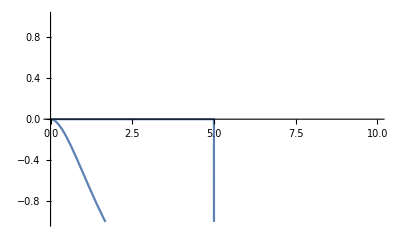

```mathematica
nsol = DSolve[{x''[t]==f0- k x[t]-2 k^(1/2) x'[t]/.{t0->5},x[0]==0,x'[0]==0},x,t]
Plot[{x[t]/.nsol,f0 HeavisideTheta[t-t0]}/.{t0->5,k->1,γ->2,f0->-2},{t,0,10},PlotRange->{{0,10},{-1,1}}]
```

```mathematica
sol = DSolve[{x''[t]==f0 HeavisideTheta[t-t0]- k x[t]-γ  Abs[x'[t]]/.{t0->5},x[0]==0,x'[0]==0},x,t];
Plot[{x[t]/.sol,f0 HeavisideTheta[t-t0]}/.{t0->5,k->1,γ->3,f0->1},{t,0,10},PlotRange->{{0,10},{-1,1}}]
```

DSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {DSolve[{x''[0.000204286]==-γ Abs[(«1»)^(«1»)[«1»]]-k x[0.000204286],x[0]==0,x'[0]==0},x,0.000204286]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {DSolve[{x''[0.000204286]==-3 Abs[(«1»)^(«1»)[«1»]]-x[0.000204286],x[0]==0,x'[0]==0},x,0.000204286]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: 0.000204286 cannot be used as a variable.

General::stop: Further output of DSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {DSolve[{x''[0.000204286]==-3. Abs[(«1»)^(«1»)[«1»]]-1. x[0.000204286],x[0.]==0.,x'[0.]==0.},x,0.000204286]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
D[-1/(2 k √(-4 k+γ^2))ⅇ^(-1/2 √(-4 k+γ^2)) f0 (-ⅇ^(γ/2+√(-4 k+γ^2)+1/2 t (-γ-√(-4 k+γ^2))) γ+ⅇ^(γ/2+1/2 t (-γ+√(-4 k+γ^2))) γ-2 ⅇ^(1/2 √(-4 k+γ^2)) √(-4 k+γ^2)+ⅇ^(γ/2+√(-4 k+γ^2)+1/2 t (-γ-√(-4 k+γ^2))) √(-4 k+γ^2)+ⅇ^(γ/2+1/2 t (-γ+√(-4 k+γ^2))) √(-4 k+γ^2)),t]
```

```mathematica
1-(  x1 y1 +x2 y2 -(x1+x2)(y1+y2)  )//Expand
```

1+x2 y1+x1 y2

```mathematica
1/2(  x1^2+x2^2 +y1^2+y2^2-(x1 y1 +x2 y2)  )//Simplify
```

1/2 (x1^2+x2^2-x1 y1+y1^2-x2 y2+y2^2)

```mathematica
Solve[{0==z^3+a z^2+b z + c/.{z->z1},1==z^3+a z^2+b z + c/.{z->z2},λ==z^3+a z^2+b z + c/.{z->z3} },{a,b,c}]
```

```mathematica
Solve[{0==a z + b/.{z->z1},1==a z + b/.{z->z2} },{a,b}]//Simplify
```

{{a→1/(-z1+z2),b→z1/(z1-z2)}}

```mathematica
a z + b/.{a->1/(-z1+z2),b->z1/(z1-z2),z->z3}//Simplify
```

(z1-z3)/(z1-z2)

```mathematica
Sum[k/n,{k,1,n}]
```

(1+n)/2

```mathematica
Solve[{0==z^3+a->1/(-z1+z2),b->z1/(z1-z2)a z^2+b z + c/.{z->z1},1==z^3+a z^2+b z + c/.{z->z2},λ==z^3+a z^2+b z + c/.{z->z3} },{a,b,c}]//Simplify
```

{{a→(z3-z2^3 z3+z2 z3^3+z1^3 (-z2+z3)-z2 λ+z1 (-1+z2^3-z3^3+λ))/((z1-z2) (z1-z3) (z2-z3)),b→((-1+z2^3) z3^2-z2^2 z3^3+z1^3 (z2^2-z3^2)+z2^2 λ-z1^2 (-1+z2^3-z3^3+λ))/((z1-z2) (z1-z3) (z2-z3)),c→(z1 (-((-1+z2^3) z3^2)+z2^2 z3^3+z1^2 z2 z3 (-z2+z3)-z2^2 λ+z1 ((-1+z2^3) z3-z2 z3^3+z2 λ)))/((z1-z2) (z1-z3) (z2-z3))}}

```mathematica
So
```

```mathematica
Simplify[1+x1 y1+x2 y1-x1^2 y1^2-2 x1 x2 y1^2-x2^2 y1^2+x1 y2+x2 y2-2 x1^2 y1 y2-4 x1 x2 y1 y2-2 x2^2 y1 y2-x1^2 y2^2-2 x1 x2 y2^2-x2^2 y2^2]
```

1+x2 (y1+y2)-x1^2 (y1+y2)^2-x2^2 (y1+y2)^2-x1 (y1+y2) (-1+2 x2 (y1+y2))

```mathematica
-1/(2 k √(-4 k+γ^2))ⅇ^(-1/2 √(-4 k+γ^2)) f0 (-ⅇ^(γ/2+√(-4 k+γ^2)+1/2 t (-γ-√(-4 k+γ^2))) γ+ⅇ^(γ/2+1/2 t (-γ+√(-4 k+γ^2))) γ-2 ⅇ^(1/2 √(-4 k+γ^2)) √(-4 k+γ^2)+ⅇ^(γ/2+√(-4 k+γ^2)+1/2 t (-γ-√(-4 k+γ^2))) √(-4 k+γ^2)+ⅇ^(γ/2+1/2 t (-γ+√(-4 k+γ^2))) √(-4 k+γ^2))+1/(2 k √(-4 k+γ^2))ⅇ^(-1/2 √(-4 k+γ^2)) f0 (-ⅇ^(γ/2+√(-4 k+γ^2)+1/2 t (-γ-√(-4 k+γ^2))) γ+ⅇ^(γ/2+1/2 t (-γ+√(-4 k+γ^2))) γ-2 ⅇ^(1/2 √(-4 k+γ^2)) √(-4 k+γ^2)+ⅇ^(γ/2+√(-4 k+γ^2)+1/2 t (-γ-√(-4 k+γ^2))) √(-4 k+γ^2)+ⅇ^(γ/2+1/2 t (-γ+√(-4 k+γ^2))) √(-4 k+γ^2)) HeavisideTheta[1-t]//Simplify
```

```mathematica
D[1/(k √(-4 k+γ^2))ⅇ^(-1/2 t (γ+√(-4 k+γ^2))) f0 (-2 ⅇ^(1/2 t (γ+√(-4 k+γ^2))) √(-4 k+γ^2)+ⅇ^(1/2 (γ+√(-4 k+γ^2))) (-γ+√(-4 k+γ^2))+ⅇ^(1/2 (γ+(-1+2 t) √(-4 k+γ^2))) (γ+√(-4 k+γ^2))),{t,2}]//FullSimplify//TrigToExp//Simplify
```

-(ⅇ^(-1/2 (-1+t) (γ+√(-4 k+γ^2))) f0 (γ-ⅇ^((-1+t) √(-4 k+γ^2)) γ+(1+ⅇ^((-1+t) √(-4 k+γ^2))) √(-4 k+γ^2)))/(√(-4 k+γ^2))

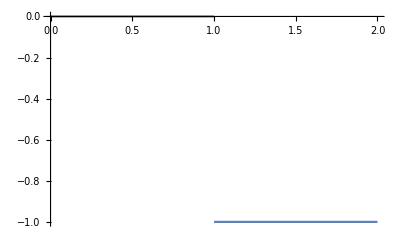

```mathematica
Plot[(-1+HeavisideTheta[1-t]),{t,0,2}]
```

```mathematica
Gq[1-x+σ+3]/Gq[1-x+σ] Gq[1-x-σ-3]/Gq[1-x-σ]
```

((1-q^(-2-x-σ)) (1-q^(-1-x-σ))^2 (1-q^(-x+σ))^3 (1-q^(1-x+σ))^2 (1-q^(2-x+σ)) Γ0q[-x+σ]^3)/((1-q)^9 Γ0q[-x-σ]^3)

```mathematica
Gq[u-3]/Gq[u]
```

((1-q^(-3+u)) (1-q^(-2+u))^2 (1-q^(-1+u))^3)/((1-q)^6 Γ0q[u]^3)

```mathematica
Gq[1-x+σ+2]/1 Gq[1-x-σ-2]/1
```

((1-q^(-1-x-σ)) (1-q^(-x+σ))^2 (1-q^(1-x+σ)) G0q[-x-σ] G0q[-x+σ] Γ0q[-x+σ]^3)/((1-q)^4 Γ0q[-x-σ])